## Exponentielle generalisée

```mathematica
Clear[ff,f,fff]
```

```mathematica
p1=0.8;p2=5;
f[x_]=Exp[-p1*Abs[x]^p2]
df[x_]=-p1*p2*Sign[x]*Abs[x]^(p2-1)*Exp[-p1*Abs[x]^p2]
ddf[x_]=(p1^2*p2^2*Abs[x]^(2*(p2-1))-p1*p2*(p2-1)*Abs[x]^(p2-1))*Exp[-p1*Abs[x]^p2]
```

ⅇ^(-0.8 Abs[x]^5)

-4. ⅇ^(-0.8 Abs[x]^5) Abs[x]^4 Sign[x]

ⅇ^(-0.8 Abs[x]^5) (-16. Abs[x]^4+16. Abs[x]^8)

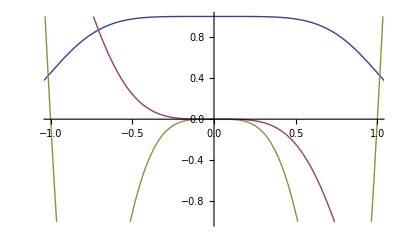

```mathematica
Plot[{f[x],df[x],ddf[x]},{x,-2,2},PlotRange->{{-1,1},{-1,1}}]
```